## What a disappointment! The J-V stuff looks truly awful

```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
orbit=1835;
```

## Initialize J-V, J_E-V data

### pot offset (in V)?

```mathematica
potTFactor=0;
```

### And the data ...

```mathematica
time={"03:02:03.055","03:02:03.372","03:02:03.688","03:02:04.004","03:02:04.321","03:02:04.637","03:02:04.954","03:02:05.270","03:02:05.586","03:02:05.903","03:02:06.219","03:02:06.535","03:02:06.852","03:02:07.168","03:02:07.485","03:02:07.801","03:02:08.117","03:02:08.434","03:02:08.750","03:02:09.067","03:02:09.383","03:02:09.699","03:02:10.016","03:02:10.332","03:02:10.648","03:02:10.965","03:02:11.281","03:02:11.598","03:02:11.914","03:02:12.230","03:02:12.547","03:02:12.863","03:02:13.180","03:02:13.496","03:02:13.812","03:02:14.129","03:02:14.445","03:02:14.762","03:02:15.078","03:02:15.394","03:02:15.711","03:02:16.027","03:02:16.343","03:02:16.660","03:02:16.976","03:02:17.293","03:02:17.609","03:02:17.925","03:02:18.242","03:02:18.558","03:02:18.875"};
pots={1128.96,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1128.96,940.80,2419.20,2222.08,1037.12,1162.56,1211.84,1350.72,1400.00,1601.60,1650.88,1951.04,1823.36,1921.92,2020.48,1671.04,1671.04,1769.60,1680.00,1868.16,1827.84,1827.84,2016.00,1827.84,1827.84,2024.96,2024.96,2024.96,2024.96,2222.08,2222.08,2024.96,1680.00,1827.84,2024.96,2024.96,1827.84,2024.96,1827.84,2016.00,2172.80,1881.60,1881.60};
curs={0.603,0.629,0.723,0.734,0.767,0.731,0.718,0.791,0.750,0.549,0.544,0.464,0.369,0.393,0.475,0.576,0.916,0.787,0.894,0.789,0.786,0.623,0.556,0.636,0.471,0.355,0.410,0.416,0.364,0.403,0.388,0.362,0.402,0.308,0.305,0.318,0.322,0.294,0.301,0.334,0.345,0.315,0.313,0.296,0.315,0.336,0.390,0.455,0.735,0.828,0.740};
curErrs={0.107,0.124,0.379,1.401,1.082,1.133,0.177,24.997,1.985,0.062,0.044,0.172,0.173,0.319,1.044,0.212,0.058,0.114,0.078,0.087,0.065,0.072,2.380,0.183,0.145,0.105,0.135,0.151,0.229,0.317,0.139,0.213,0.177,0.070,0.291,0.242,0.072,0.125,9.041,17.708,0.236,0.143,0.147,0.161,0.115,0.083,0.431,0.097,0.061,0.052,0.079};
jes={0.652,0.709,0.853,0.851,0.924,0.887,0.873,0.947,0.887,0.568,0.523,0.453,0.344,0.378,0.472,0.606,1.066,0.998,1.189,1.145,0.999,0.804,0.721,0.752,0.555,0.418,0.470,0.476,0.387,0.464,0.465,0.414,0.460,0.344,0.343,0.362,0.339,0.305,0.340,0.386,0.406,0.375,0.348,0.317,0.336,0.392,0.450,0.587,1.154,1.439,1.342};
jeErrs={0.354,0.383,1.252,2.658,2.500,2.728,0.569,51.719,3.141,0.239,0.149,1.731,0.568,15.366,1.575,0.777,0.583,1.455,0.972,7.767,0.378,0.383,0.646,5.676,2.944,1.953,0.307,0.958,0.853,1.351,2.406,1.215,1.371,0.537,0.795,0.883,0.378,0.386,5.343,10.210,5.122,0.462,0.433,2.054,0.262,0.526,11.947,0.408,0.315,0.668,0.530};
gaussbulkEs={894.71,1383.08,1320.59,914.75,1010.82,1288.71,1104.87,1297.89,1357.74,984.71,621.57,1038.86,813.46,852.38,834.02,866.62,1179.46,1175.73,1531.23,1661.48,1169.64,1295.19,1353.85,1059.22,953.66,1273.83,692.44,808.38,831.60,1002.26,1284.96,1111.04,974.57,997.79,1060.02,989.50,877.30,913.37,1069.66,983.39,706.06,1037.62,868.12,622.18,855.20,1011.58,967.36,992.79,1435.38,1387.99,2242.52};
kappabulkEs={1205.24,1156.29,1074.68,1079.30,1108.09,1089.31,1027.54,1165.64,1154.18,863.50,669.67,957.17,760.22,700.77,997.69,1173.78,1083.98,876.15,1275.77,1190.90,966.55,815.36,1047.09,689.96,816.89,1083.59,929.96,870.86,934.95,919.87,1090.42,916.53,883.91,926.46,854.59,876.49,743.58,728.26,904.00,875.79,875.34,889.01,767.46,758.89,713.47,866.20,912.99,1115.20,1053.05,1883.71,1923.15};
```

## Manip plots to decide on indices to use

### Check out J-V relation

```mathematica
ind1Start=1;ind1End=19;ind1Init=5;ind2Init=20;(*Jim alt?*)
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],AxesStyle->(FontSize->24),PlotRange->{{000,Max[pots]*1.1},{0,Max[curs]*1.1}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

### Check out energy flux–voltage relation

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,Max[pots]*1.1},{0,Max[jes]*1.2}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

Part::take: Cannot take positions 116 through 131 in {1128.96,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1128.96,940.8,2419.2,2222.08,1037.12,1162.56,1211.84,1350.72,1400.,1601.6,1650.88,1951.04,1823.36,1921.92,2020.48,1671.04,1671.04,1769.6,1680.,1868.16,1827.84,1827.84,2016.,1827.84,1827.84,2024.96,2024.96,2024.96,2024.96,2222.08,2222.08,2024.96,1680.,1827.84,2024.96,2024.96,1827.84,2024.96,1827.84,2016.,2172.8,1881.6,«1»}.

Part::take: Cannot take positions 116 through 131 in {0.652,0.709,0.853,0.851,0.924,0.887,0.873,0.947,0.887,0.568,0.523,0.453,0.344,0.378,0.472,0.606,1.066,0.998,1.189,1.145,0.999,0.804,0.721,0.752,0.555,0.418,0.47,0.476,0.387,0.464,0.465,0.414,0.46,0.344,0.343,0.362,0.339,0.305,0.34,0.386,0.406,0.375,0.348,0.317,0.336,0.392,0.45,0.587,1.154,1.439,«1»}.

Part::take: Cannot take positions 116 through 131 in {0.354,0.383,1.252,2.658,2.5,2.728,0.569,51.719,3.141,0.239,0.149,1.731,0.568,15.366,1.575,0.777,0.583,1.455,0.972,7.767,0.378,0.383,0.646,5.676,2.944,1.953,0.307,0.958,0.853,1.351,2.406,1.215,1.371,0.537,0.795,0.883,0.378,0.386,5.343,10.21,5.122,0.462,0.433,2.054,0.262,0.526,11.947,0.408,0.315,0.668,«1»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[{1128.96,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1128.96,940.8,2419.2,2222.08,1037.12,1162.56,1211.84,1350.72,1400.,1601.6,1650.88,1951.04,1823.36,1921.92,2020.48,1671.04,1671.04,1769.6,1680.,1868.16,1827.84,1827.84,2016.,1827.84,1827.84,2024.96,2024.96,2024.96,2024.96,2222.08,2222.08,2024.96,1680.,1827.84,2024.96,2024.96,1827.84,2024.96,1827.84,2016.,2172.8,1881.6,«1»}⟦116;;131⟧,{0.652,0.709,0.853,«45»,1.154,1.439,«1»}⟦«1»⟧].

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

Part::pkspec1: The expression ErrorBar[116;;131] cannot be used as a part specification.

Riffle::list: List expected at position 1 in Riffle[Riffle[Riffle[{1128.96,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1128.96,940.8,2419.2,2222.08,1037.12,1162.56,1211.84,1350.72,1400.,1601.6,1650.88,1951.04,1823.36,1921.92,2020.48,1671.04,1671.04,1769.6,1680.,1868.16,1827.84,1827.84,2016.,1827.84,1827.84,2024.96,2024.96,2024.96,2024.96,2222.08,2222.08,2024.96,1680.,1827.84,2024.96,2024.96,1827.84,2024.96,1827.84,2016.,2172.8,1881.6,«1»}⟦116;;131⟧,{0.652,0.709,«48»,«1»}⟦«1»⟧]],«1»].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

Part::partw: Part {116,131} of {03:02:03.055,03:02:03.372,03:02:03.688,03:02:04.004,03:02:04.321,03:02:04.637,03:02:04.954,03:02:05.270,03:02:05.586,03:02:05.903,03:02:06.219,03:02:06.535,03:02:06.852,03:02:07.168,03:02:07.485,03:02:07.801,03:02:08.117,«17»,03:02:13.812,03:02:14.129,03:02:14.445,03:02:14.762,03:02:15.078,03:02:15.394,03:02:15.711,03:02:16.027,03:02:16.343,03:02:16.660,03:02:16.976,03:02:17.293,03:02:17.609,03:02:17.925,03:02:18.242,03:02:18.558,«1»} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[Riffle[{03:02:03.055,03:02:03.372,03:02:03.688,03:02:04.004,03:02:04.321,03:02:04.637,03:02:04.954,03:02:05.270,03:02:05.586,03:02:05.903,03:02:06.219,03:02:06.535,03:02:06.852,03:02:07.168,03:02:07.485,03:02:07.801,«19»,03:02:14.129,03:02:14.445,03:02:14.762,03:02:15.078,03:02:15.394,03:02:15.711,03:02:16.027,03:02:16.343,03:02:16.660,03:02:16.976,03:02:17.293,03:02:17.609,03:02:17.925,03:02:18.242,03:02:18.558,«1»}⟦{116,«3»}⟧,«3»]].

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

General::stop: Further output of Riffle::argtu will be suppressed during this calculation.

Part::pkspec1: The expression ErrorBar[116;;131] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: Riffle[Riffle[Riffle[Riffle[{{1.,1128.96},{2.,1128.96},{3.,1379.84},{4.,1379.84},{5.,1379.84},{6.,1379.84},{7.,1379.84},{8.,1379.84},{9.,1128.96},{10.,940.8},{11.,2419.2},{12.,2222.08},{13.,1037.12},{14.,1162.56},{15.,1211.84},«21»,{37.,2024.96},{38.,2222.08},{39.,2222.08},{40.,2024.96},{41.,1680.},{42.,1827.84},{43.,2024.96},{44.,2024.96},{45.,1827.84},{46.,2024.96},{47.,1827.84},{48.,2016.},{49.,2172.8},{50.,1881.6},«1»}⟦116;;131⟧,«1»]],«1»]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

The fits—J-V, J_E-V, and combined

## Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
inds1=Range[40,57];
```

```mathematica
inds2=Range[116,131];
```

```mathematica
inds3={3,4}~Join~inds2;
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorJe1,errorJe2,errorJe3}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

## Fits: Select indices to use, setup bounds and initial guesses

### Which to use?

```mathematica
useinds1=0; (*Else use inds2*)
```

### Bounds

```mathematica
minFitT=10;
maxFitT=5000;
minFitRB=3;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

#### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds2 ...

## Nonlinear J-V fits

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,10<kFitT<4000,3<kFitRB<1000000,1.501<kFitKappa<20};
gConstraints={0.01<gFitN<10,10<gFitT<4000,3<gFitRB<1000000};*)
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[jData,{kModel,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts];
```

```mathematica
gFit=NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
```

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
```

## Nonlinear J_E-V fits

### Initial guesses

```mathematica
(*kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;*)
```

```mathematica
(*gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;*)
```

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};*)
```

```mathematica
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFitJeV=NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts];
```

```mathematica
gFitJeV=NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
```

```mathematica
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
```

## Now J-V and J_E-V fits simultaneously!

```mathematica
(*RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;*)
```

```mathematica
(*RBinit=kBestJeVRB;Tminit=kBestJeVT;nminit=kBestJeVN;kappainit=kBestJeVKappa;*)
```

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];
```

```mathematica
gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts];
```

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts];
```

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
```

```mathematica
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};
```

Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=1200;(*maxPot=Max[pots[[;;]]];*)
```

```mathematica
minJ=0;maxJ=2.5;
```

```mathematica
minJe=0;maxJe=2.5;
```

### Setup combined fit plots

```mathematica
parNames={"T_m : ","n_m : ","R_B : ","χ_red^2:"};
vSpace=0.5;
pTableFontSize=16;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJVVals~Join~{""}~Join~kJVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJeVVals~Join~{""}~Join~kJeVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gCombVals~Join~{""}~Join~kCombVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[{0.12,0.7}]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref=ToString@StringForm["Orb`1`",orbit];
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
```

```mathematica
(*combJVPref="combJVJeVFit__JV";
combJeVPref="combJVJeVFit__JeV";*)
```

```mathematica
(*{JVFilename,JeVFilename,combJVFilename,combJeVFilename}=(ToString@StringForm["`1`__`2`__inds_`3`-`4`.png",orbPref,#,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combJVPref,combJeVPref}*)
```

```mathematica
If[potTFactor == 0,suffString="",suffString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

```mathematica
{JVFilename,JeVFilename,combFilename}=(ToString@StringForm["`1`__`2``3`__inds_`4`-`5`.png",orbPref,#,suffString,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combPref}
```

{Orb3760__JVFit__inds_116-131.png,Orb3760__JeVFit__inds_116-131.png,Orb3760__combJVJeVFit__inds_116-131.png}

### J-V plot

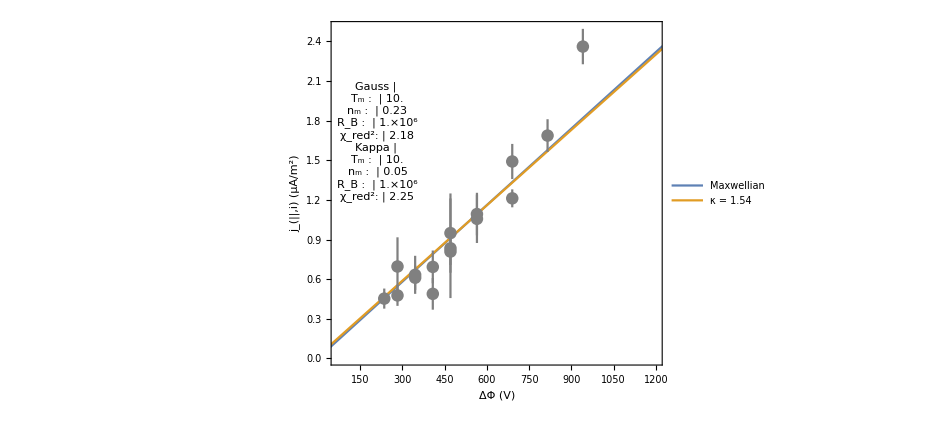

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

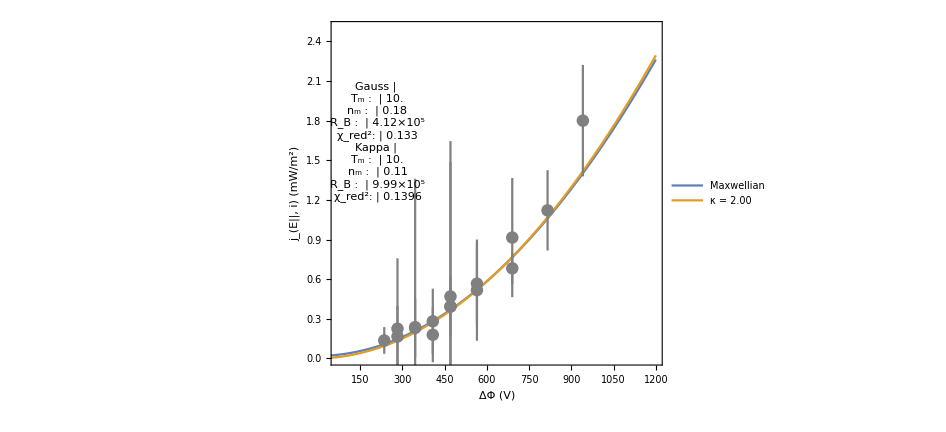

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

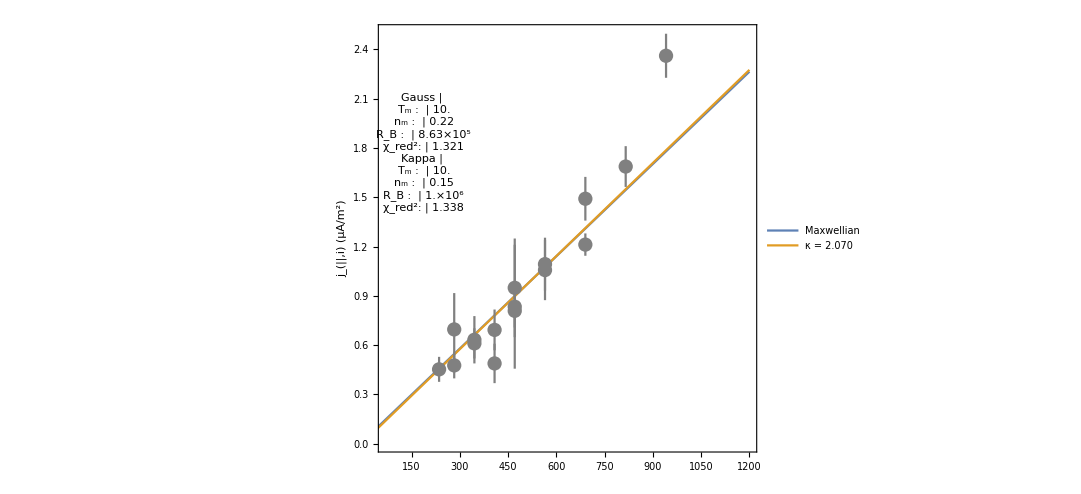
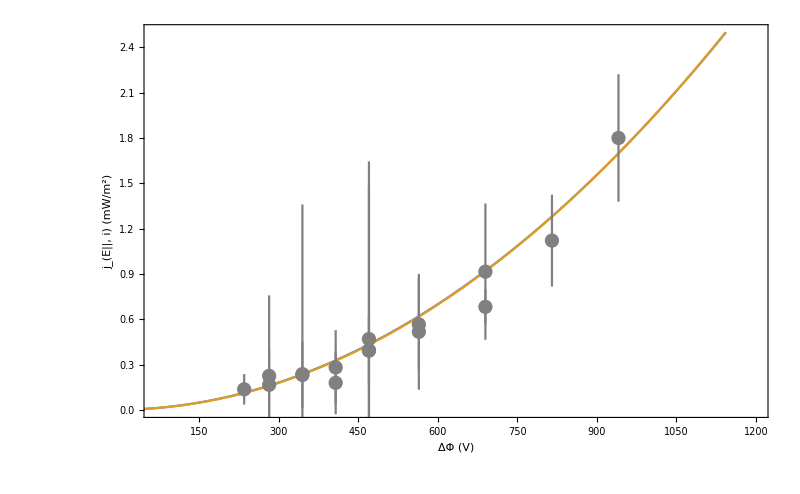

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

```mathematica
makePlots=1;
```

```mathematica
(*If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Export[dir<>JeVFilename,JeVPlot];Export[dir<>combJVFilename,combJVPlot];Export[dir<>combJeVFilename,combJeVPlot];Print["Done!"]]*)
```

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180320/ ...

Orb3760__JeVFit__inds_116-131.png ...

Orb3760__combJVJeVFit__inds_116-131.png ...

Done!

Now everything at once

### Bounds

```mathematica
minFitT=80;
maxFitT=1000;
minFitRB=3;
maxFitRB=100000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

### Setup indices

```mathematica
indsSeg1=Range[40,57];
```

```mathematica
indsSeg2=Range[116,131];
```

```mathematica
(*indsSeg2=Range[162,198]; (*Alt*)*)
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{jDataSeg1,jDataSeg2}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jErrDataSeg1,jErrDataSeg2}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jWtsSeg1,jWtsSeg2}=(1/(curErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

Energy flux data

```mathematica
{jeDataSeg1,jeDataSeg2}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeErrDataSeg1,jeErrDataSeg2}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeWtsSeg1,jeWtsSeg2}=(1/(jeErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDatSeg1 = Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y}];
```

```mathematica
combDatSeg2 = Join[jDataSeg2/.{x_,y_}->{1,x,y},jeDataSeg2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWtsSeg1=jWtsSeg1~Join~jeWtsSeg1;
```

```mathematica
combWtsSeg2=jWtsSeg2~Join~jeWtsSeg2;
```

```mathematica
doubledDat= Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y},jDataSeg2/.{x_,y_}->{3,x,y},jeDataSeg2/.{x_,y_}->{4,x,y}];
```

```mathematica
doubledWts=jWtsSeg1~Join~jeWtsSeg1~Join~jWtsSeg2~Join~jeWtsSeg2;
```

### Now the doubled double model

```mathematica
kDoubledFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==3,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa],set==4,Evaluate@JEVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gDoubledFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==3,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN],set==4,Evaluate@JEVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kDoubledFit=NonlinearModelFit[doubledDat,{kDoubledFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kDoubledConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB1,kFitRB1init},{kFitRB2,kFitRB2init},{kFitKappa,kFitKappainit}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,(«1»)/((1-1/(«19»)) «1» Gamma[«1»]),set==2,(«1»)/(«1»),«1»,(«1»)/(«1»),set==4,(0.0000268059 «6» Gamma[1+2.12064])/((-2+2.12064) (-1+2.12064) Gamma[-1/2+2.12064])]]

```mathematica
gDoubledFit=NonlinearModelFit[doubledDat,{gDoubledFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gDoubledConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB1,gFitRB1init},{gFitRB2,gFitRB2init}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,«6»,0.0000268059 0.504655 99913.5 80.^(3/2) (2+pot/80.-ⅇ^(-pot/((-1+99913.5) «18»)) (2 (1-1/99913.5)+pot/80.))]]

```mathematica
kDOF=Length[doubledDat[[;;,1]]]-4;
```

```mathematica
gDOF=Length[doubledDat[[;;,1]]]-3;
```

```mathematica
{kDoubledN,kDoubledT,kDoubledRB1,kDoubledRB2,kDoubledKappa,kDoubledChi2red}=Values@kDoubledFit["BestFitParameters"]~Join~{Total[(kDoubledFit["FitResiduals"])^2*doubledWts]/kDOF};
```

```mathematica
{gDoubledN,gDoubledT,gDoubledRB1,gDoubledRB2,gDoubledChi2red}=Values@gDoubledFit["BestFitParameters"]~Join~{Total[(gDoubledFit["FitResiduals"])^2*doubledWts]/gDOF};
```

### Now setup plots

```mathematica
(*Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]*)
```

```mathematica
(*JVPlotSeg1=Show[Plot[{JVMaxwellian[pot,gDoubledRB1,gDoubledT,gDoubledN],JVKappa[pot,kDoubledRB1,kDoubledT,kDoubledN,kDoubledKappa]},{pot,minPot,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kDoubledKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23]],ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]]*)
```

```mathematica
doubledRepl={gRB1->gDoubledRB1,gRB2->gDoubledRB2,gTm->gDoubledT,gnm->gDoubledN,gChi2->gDoubledChi2red,kRB1->kDoubledRB1,kRB2->kDoubledRB2,kTm->kDoubledT,knm->kDoubledN,kappa->kDoubledKappa,kChi2->kDoubledChi2red};
```

```mathematica
gDoubledVals1=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB1,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals1=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB1,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
gDoubledVals2=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB2,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals2=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB2,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
doubledParTable1=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gDoubledVals1~Join~{""}~Join~kDoubledVals1}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledParTable2=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gDoubledVals2~Join~{""}~Join~kDoubledVals2}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledTitle1=StringJoin@Riffle[time[[indsSeg1[[{1,-1}]]]],"–"];
```

```mathematica
doubledTitle2=StringJoin@Riffle[time[[indsSeg2[[{1,-1}]]]],"–"];
```

```mathematica
doubledFitJVPlot1=Plot[Evaluate@(({JVMaxwellian[pot,gRB1,gTm,gnm],JVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",doubledTitle1],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable1,Scaled[{0.12,0.7}]]];
```

```mathematica
doubledFitJeVPlot1=Plot[Evaluate@(({JEVMaxwellian[pot,gRB1,gTm,gnm],JEVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
doubledFitJVPlot2=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm],JVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.doubledRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",doubledTitle2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[{0.12,0.7}]]];
```

```mathematica
doubledFitJeVPlot2=Plot[Evaluate@(({JEVMaxwellian[pot,gRB2,gTm,gnm],JEVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
doubledJVPlot1=Show[doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot1=Show[doubledFitJeVPlot1,ErrorListPlot[jeErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJVPlot2=Show[doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot2=Show[doubledFitJeVPlot2,ErrorListPlot[jeErrDataSeg2,PlotStyle->Gray]];
```

### Now show plots

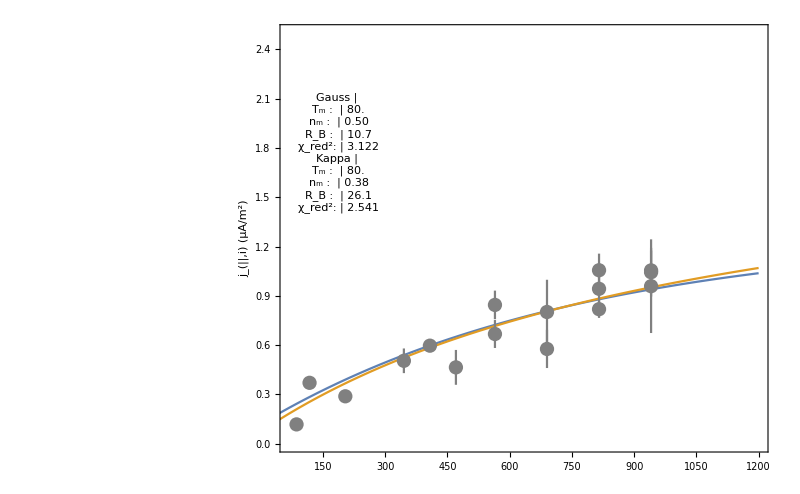
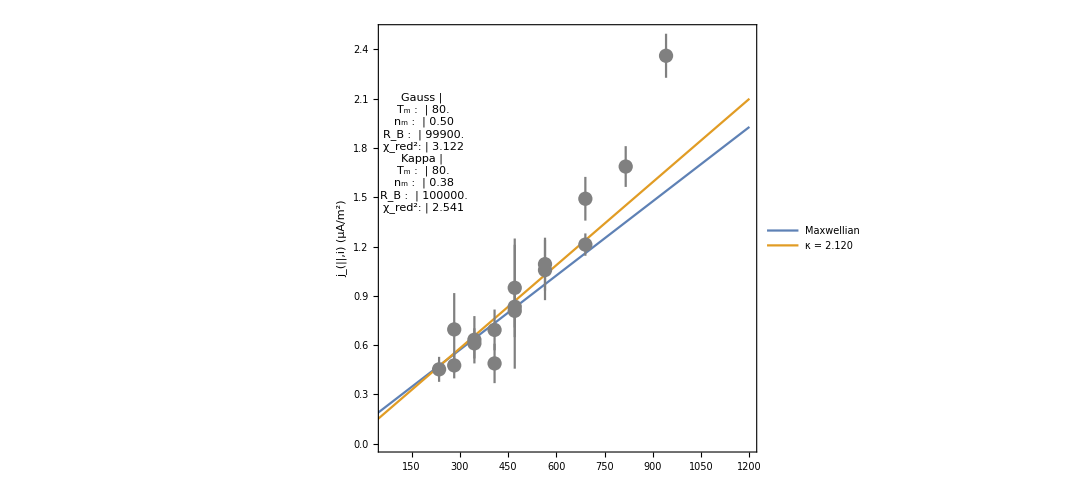
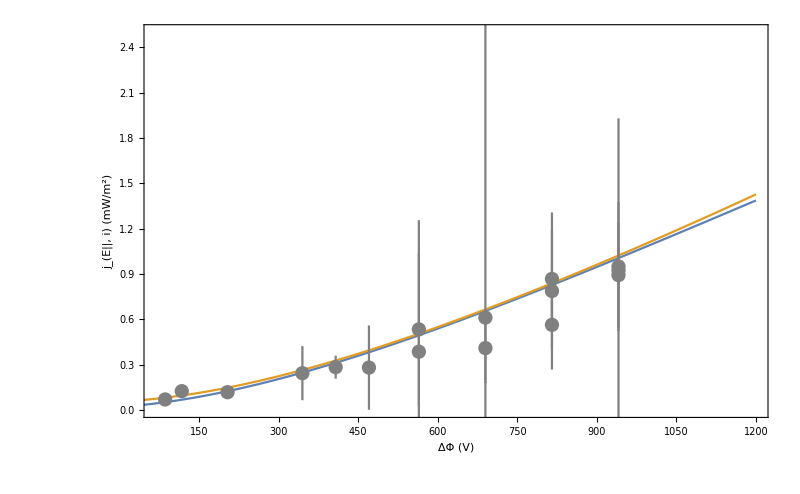
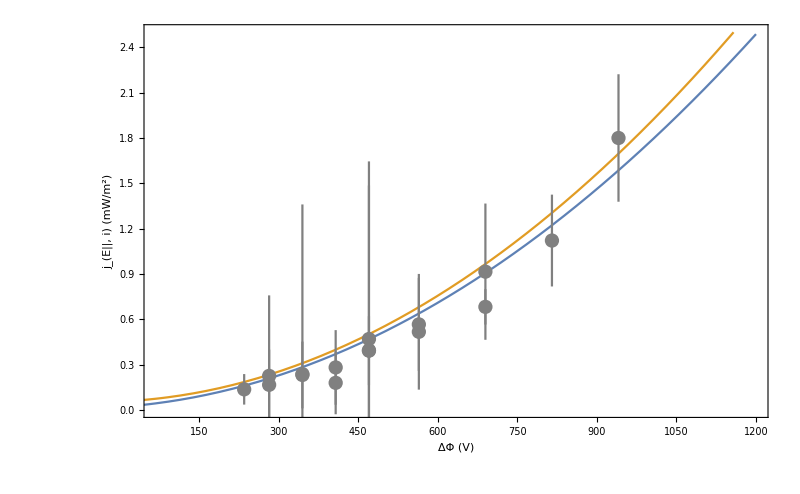
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
doubledPlot=Grid[{{doubledJVPlot1,doubledJVPlot2},{doubledJeVPlot1,doubledJeVPlot2}}]
```

Param tables

### J-V params

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.0512934 | 7.01681 | 0.00731006 | 0.994288
kFitT | 10.0009 | 27869.6 | 0.000358847 | 0.99972
kFitRB | 999995. | 5.20248 | 192215. | 2.64818×10^-58
kFitKappa | 1.54131 | 130.222 | 0.0118361 | 0.990751

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.225203 | 1.73466 | 0.129825 | 0.898692
gFitT | 10. | 167.075 | 0.0598532 | 0.953183
gFitRB | 999839. | 1.2243×10^10 | 0.0000816662 | 0.999936

### J_E-V params

```mathematica
kFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.114541 | 9.18081 | 0.0124762 | 0.990251
kFitT | 10.0002 | 1649.44 | 0.00606279 | 0.995262
kFitRB | 999008. | 9.64825×10^9 | 0.000103543 | 0.999919
kFitKappa | 2.00408 | 1.4256 | 1.40578 | 0.18515

```mathematica
gFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.184888 | 0.865894 | 0.213523 | 0.834232
gFitT | 10.0005 | 108.707 | 0.0919948 | 0.928105
gFitRB | 412477. | 2.36883×10^9 | 0.000174127 | 0.999864

### Params from combined fit

```mathematica
kCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitRB | 999918. | 2.06162×10^9 | 0.000485016 | 0.999616
kFitT | 10. | 140.718 | 0.0710643 | 0.943852
kFitN | 0.145846 | 1.44933 | 0.10063 | 0.920561
kFitKappa | 2.07156 | 7.44902 | 0.278099 | 0.78298

```mathematica
gCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitRB | 450860. | 4.64319×10^9 | 0.0000971014 | 0.999923
gFitT | 20. | 30.7434 | 0.650545 | 0.518801
gFitN | 0.738934 | 0.408339 | 1.80961 | 0.0773503